```mathematica
M=1;
Λ=1;
g=2;
f[x_]=1/Λ*(g(SphericalBesselJ[0,x])^2)/(1+g*x*SphericalBesselJ[0,x]*SphericalBesselY[0,x]-I*g*x*(SphericalBesselJ[0,x])^2);
cotd[x_]=1/(f[x]*x)+I;
del[x_]=ArcCot[cotd[x]];
scatlen =-del[0.0001]/0.0001
```

2.+0. ⅈ

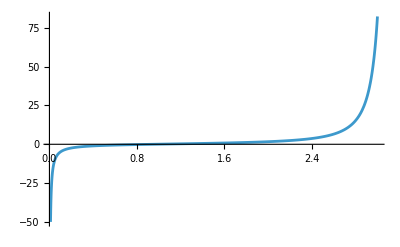

```mathematica
Plot[{cotd[x]},{x,0.01,3},PlotRange->All]
```

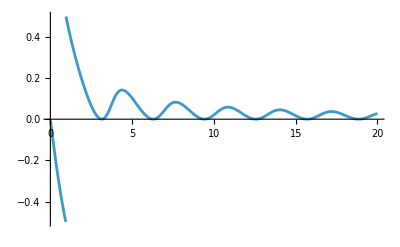

```mathematica
Plot[{del[x]/Pi},{x,0.01,20},PlotRange->All]
```

```mathematica
root1=Re[z/.FindRoot[{cotd[z]==0},{z,0.1}]]
```

0.947747

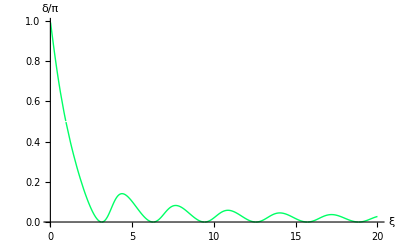

```mathematica
delta=Plot[Piecewise[{{1+del[z]/Pi,z<root1}},del[z]/Pi],{z,0.01,20},PlotRange->All,AxesLabel->{"ξ","δ/π"},PlotStyle->{Hue[0.4],Thick},LabelStyle->Medium]
```

```mathematica
ComplexPlot3D[f[x],{x,-5-3I,5+3I}]
```

-Graphics3D-

```mathematica
NSolve[1/f[z]==0,z]
```

NSolve::fexp: Warning: NSolve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{{z→0.+0.796812 ⅈ},{z→-3.71186-0.703552 ⅈ},{z→-6.9289-0.98762 ⅈ},{z→-10.1045-1.16774 ⅈ},{z→-13.2659-1.3 ⅈ},{z→-16.4207-1.40457 ⅈ},{z→-19.5717-1.49106 ⅈ},{z→-22.7203-1.5648 ⅈ},{z→-25.8675-1.62906 ⅈ},{z→-29.0136-1.68602 ⅈ},{z→-32.1589-1.73715 ⅈ},{z→-35.3036-1.78354 ⅈ},{z→-38.4478-1.826 ⅈ},{z→-41.5917-1.86513 ⅈ},{z→-44.7353-1.90143 ⅈ},{z→-47.8787-1.93527 ⅈ}}